### Preliminary

```mathematica
$HistoryLength=4;
```

```mathematica
ma=6.015122 ;
mi=170.936323 ;
μ=Sqrt[ma/mi];
```

Let’s write a module for plotting from a file

```mathematica
MakePlot[file_,xcol_,ycols_,prange_,flabel_,otheroptions_]:=Module[
{AllData,PlotData,Ncols},
AllData=Transpose[Import[file]];
Ncols=Dimensions[AllData][[1]];
PlotData=Table[Transpose[{AllData[[xcol]],AllData[[ycol]]}],{ycol,ycols}];
ListPlot[PlotData, Joined->True,Frame->True,PlotTheme->None,LabelStyle->{16},PlotStyle->{Black,Red,Green,Blue,Purple},GridLines->Automatic,GridLinesStyle->Thin,PlotRange->prange,FrameLabel->flabel,otheroptions]
]
```

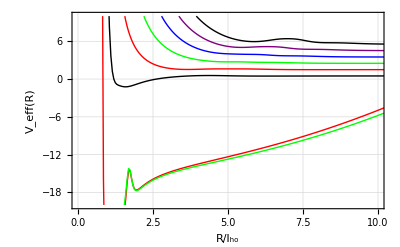

```mathematica
MakePlot["/Users/niravmehta/Documents/GitHub/AtomIon1D/QuickEffV.dat",1,{2,3,4,5,6,7,8,9},{{0,10},{-20,10}},{"R/l_ho","V_eff(R)"},{}]
```

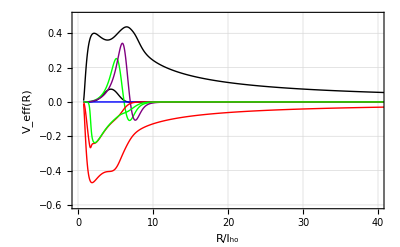

```mathematica
MakePlot["/Users/niravmehta/Documents/GitHub/AtomIon1D/QuickPMat.dat",1,{2,3,4,5,6,7,8,9},{{0,40},{-.6,.5}},{"R/l_ho","V_eff(R)"}]
```

### Some data

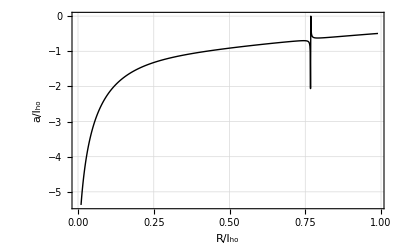

```mathematica
MakePlot["/Users/niravmehta/Documents/GitHub/AtomIon1D/MyCABA/Observables.dat",1,{2},All,{"R/l_ho","a/l_ho"}]
```

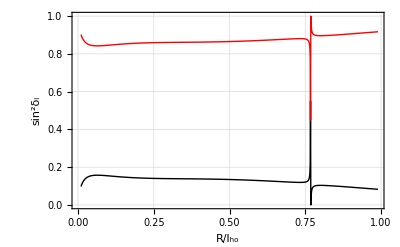

```mathematica
MakePlot["/Users/niravmehta/Documents/GitHub/AtomIon1D/MyCABA/Observables.dat",1,{3,4},All,{"R/l_ho","sin^2δ_l"}]
```

```mathematica
rawcurves=Import["/Users/niravmehta/Documents/GitHub/AtomIon1D/QuickEffV.dat"];
```

```mathematica
Dimensions[rawcurves][[2]]
```

9

```mathematica
Transpose[rawcurves][[2]];
```

```mathematica
U1Dat=Transpose[{Transpose[rawcurves][[1]],Transpose[rawcurves][[2]]}];
```

```mathematica
Dimensions[rawcurves]
```

{1000,13}

```mathematica
rawcurves[[1]]
```

{50.,0.499992,1.49999,2.5,3.50001,4.50002,5.50005,6.50008,7.50012,36.5154,37.5167,38.0833,39.062}

```mathematica
U1[x_]:=Interpolation[U1Dat][x]
```

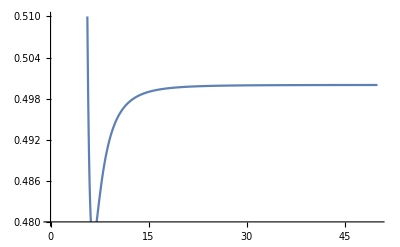

```mathematica
Plot[U1[x],{x,.75,50},PlotRange->{0.48,.51}]
```

For the even states:

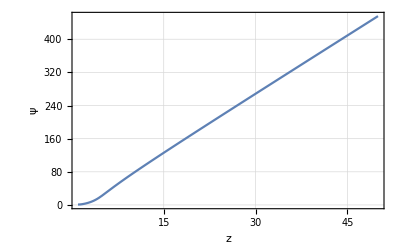

```mathematica
Clear[ψ];ϵ=0.5;ψ=ψ/.NDSolve[{-1/(2 μ)ψ''[z]+U1[z] ψ[z]==ϵ ψ[z],ψ[1]==1,ψ'[1]==0},ψ,{z,0.75,50}][[1]];
Plot[ψ[z],{z,1,50},Frame->True,GridLines->Automatic,LabelStyle->Large,FrameLabel->{"z","ψ"}]
```

```mathematica
Solve[{A u1==Sin[k x1]+TanDelta Cos[k x1],A u2==Sin[k x2]+TanDelta Cos[k x2]},{A,TanDelta}]//Simplify
```

{{A→-Sin[k (x1-x2)]/(u2 Cos[k x1]-u1 Cos[k x2]),TanDelta→(-u2 Sin[k x1]+u1 Sin[k x2])/(u2 Cos[k x1]-u1 Cos[k x2])}}

```mathematica
CalcTanDelta[Εtest_,xmax_,xmin_,μ_,V_]:=
Module[{TanDelta,sol,k,u1,u2,x1,x2,u},
x1=0.95 xmax;
x2=0.99xmax;
k=√(2 μ Εtest);
sol=NDSolve[{-1/(2 μ)u''[x]+V[x] u[x]==Εtest u[x],u[xmin]==0.001,u'[xmin]==0},u,{x,xmin,xmax}];
u1=u[x1]/.sol[[1]];
u2=u[x2]/.sol[[1]];
TanDelta=(-u2 Sin[k x1]+u1 Sin[k x2])/(u2 Cos[k x1]-u1 Cos[k x2]);
Return[TanDelta]
]
```

```mathematica
CalcERE[xmin_,xmax_,ΕMin_,ΕMax_,μ_,V_,NumE_]:=
Module[{EREData,ascat,reff,A,B,fitpars,dE,ksqr,adata},
dE=(ΕMax-ΕMin)/NumE;
EREData=Table[{2μ Εtest,√(2μ Εtest)/CalcTanDelta[Εtest,xmax,xmin,μ,V]},{Εtest,ΕMin,ΕMax,dE}];
adata=Table[{Εtest,-CalcTanDelta[Εtest,xmax,xmin,μ,V]/(√(2μ Εtest))},{Εtest,ΕMin,ΕMax,dE}];
fitpars=FindFit[EREData,A+B ksqr,{A,B},ksqr];
ascat=-1/A/.fitpars;
reff=2B/.fitpars;
Return[{ascat,reff,EREData,adata}]
]
```

```mathematica
Urel[x]=U1[x]-0.5
```

-0.5+InterpolatingFunction[…][x]

```mathematica
kcotdel=CalcERE[.75,50.0,0.01,0.99,μ,Urel,100];
```

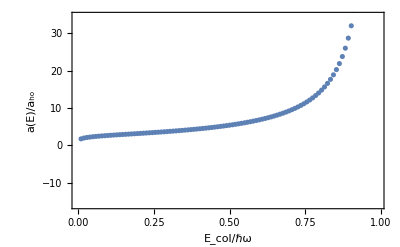

```mathematica
pMathematica1chan=ListPlot[kcotdel[[4]],Frame->True,FrameLabel->{"E_col/ℏω","a(E)/a_ho"}]
```

```mathematica
CABA12chan=Import["/Users/niravmehta/Documents/GitHub/AtomIon1D/MyCABA/Observables.dat"];
CABA12chan=Transpose[Drop[Transpose[CABA12chan],{3,4}]];
```

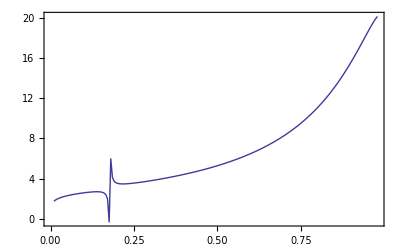

```mathematica
ListPlot[CABA12chan,Joined->True,PlotTheme->None,Frame->True]
```

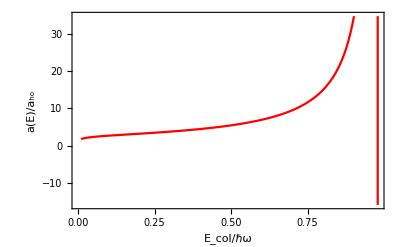

```mathematica
pcaba1chan=ListPlot[CABA1chan,Frame->True,FrameLabel->{"E_col/ℏω","a(E)/a_ho"},Joined->True,PlotStyle->Red]
```

```mathematica
CABA6chan=Import["/Users/niravmehta/Documents/GitHub/AtomIon1D/MyCABA/CABA1BS-6chan.dat"];
CABA6chan=Transpose[Drop[Transpose[CABA6chan],{3}]];
```

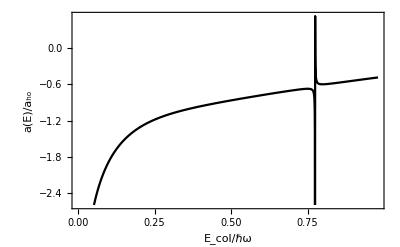

```mathematica
pcaba6chan=ListPlot[CABA6chan,Frame->True,FrameLabel->{"E_col/ℏω","a(E)/a_ho"},Joined->True,PlotStyle->Black]
```

```mathematica
Show[pcaba6chan,pMathematica1chan]
```

-Graphics-

```mathematica
Cos[π-α]
```

-Cos[α]

```mathematica
1/Tan[θc]
```

5.33083

```mathematica
1.07*3400
```

3638.

```mathematica
TrigExpand[Cos[a+b]]
```

Cos[a] Cos[b]-Sin[a] Sin[b]

```mathematica
Cos[π-ϕ]
```

-Cos[ϕ]

```mathematica
Sin[π-ϕ]
```

Sin[ϕ]

```mathematica
3645/3400.
```

1.07206

```mathematica
GegenbauerC[λ,0,x]
```

0

```mathematica
-2!!
```

-2

## Bound states

Let’s take a look at the bound states that live in the quadratic potential curves to see if they line up with the resonances.

```mathematica
EffVData=Transpose[Import["/Users/niravmehta/Documents/GitHub/AtomIon1D/QuickEffV.dat"]];
```

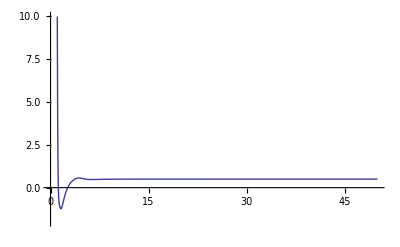

```mathematica
ListPlot[Transpose[{EffVData[[1]],EffVData[[2]]}],Joined->True,PlotRange->{-2,10},PlotTheme->None]
```

```mathematica
RawP
```

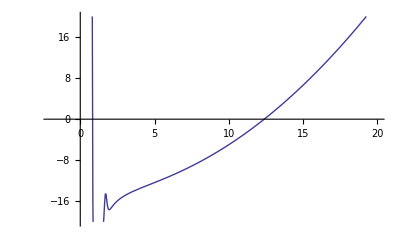

```mathematica
ListPlot[Transpose[{EffVData[[1]],EffVData[[8]]}],Joined->True,PlotRange->{{-2,20},{-20,20}},PlotTheme->None]
```

```mathematica
VeffBound1=Interpolation[Transpose[{EffVData[[1]],EffVData[[8]]}]]
```

InterpolatingFunction[…]

```mathematica
VeffBound2=Interpolation[Transpose[{EffVData[[1]],EffVData[[9]]}]]
```

InterpolatingFunction[…]

```mathematica
{vals,vecs}=NDEigensystem[{-1/(2μ)F''[R]+(VeffBound1[R]+200)F[R],DirichletCondition[F[R]==0,True]},F[R],{R,0.75,40},20,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->.1}}}];
```

```mathematica
vals-200
```

{-15.9619,-12.0011,-9.50558,-7.20881,-4.99077,-2.81563,-0.668014,1.46008,3.57336,5.67484,7.76656,9.85002,11.9263,13.9963,16.0608,18.1204,20.1757,22.227,24.2746,26.3188}

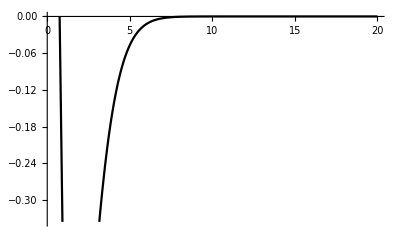

```mathematica
Plot[vecs[[1]],{R,0.2,20}]
```

```mathematica
{vals,vecs}=NDEigensystem[{(-1/(2μ)F''[R]+(VeffBound2[R]+200)F[R]),DirichletCondition[F[R]==0,True]},F[R],{R,0.5,40},20];
```

```mathematica
vals-200
```

{-13.4342,-11.0655,-8.81239,-6.48795,-3.96052,-1.49481,0.528831,3.41553,5.80493,8.56718,11.212,14.0609,16.6995,19.7561,22.2382,25.3293,27.9201,30.7471,34.1176,36.3081}

InterpolatingFunction::dmval: Input value {0.301015} lies outside the range of data in the interpolating function. Extrapolation will be used.

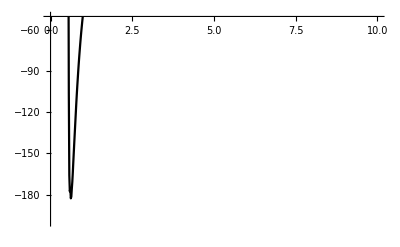

```mathematica
Plot[VeffBound2[R],{R,0.3,50},PlotRange->{{0,10},{-200,-50}}]
```